{{2,53},{-2,5},{2.87446,0.953009},{2.23609,-0.0000311614}}

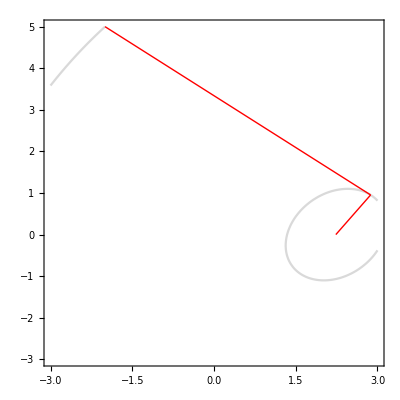

{2,53}

{2.23609,-0.0000311614}

{2,81}

{2.23607,-8.02405×10^-8}

```mathematica
F1[x_,y_]:=10 x^2-4x y+7 y^2-4 √5(5x-y)-16;
F2[x_,y_]:=(x^2-y)^2+(x-1)^2;
F3[x_,y_]:=5*(x^2-y)^2+(x-1)^2;
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps1f1p1.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-3,3},{y,-3,5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps2f1p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

```mathematica
{2,55}
```

{2,55}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps1f1p1.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-3,3},{y,-3,5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps2f1p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

{{2,53},{-2,5},{2.87446,0.953009},{2.23609,-0.0000311614}}

-Graphics-

{2,53}

{2.23609,-0.0000311614}

{2,81}

{2.23607,-8.02405×10^-8}

{{2,53},{-2,5},{2.87446,0.953009},{2.23604,0.000045853}}

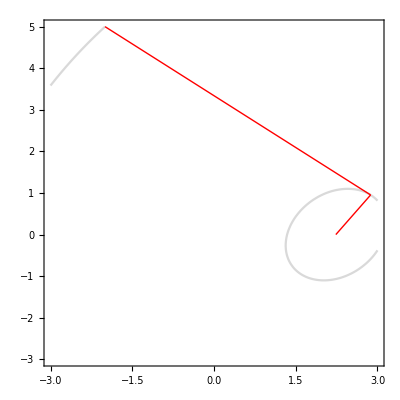

{2,53}

{2.23604,0.000045853}

{2,81}

{2.23607,3.14413×10^-8}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps1f1p1.txt","Table"]
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,-3,3},{y,-3,5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps2f1p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

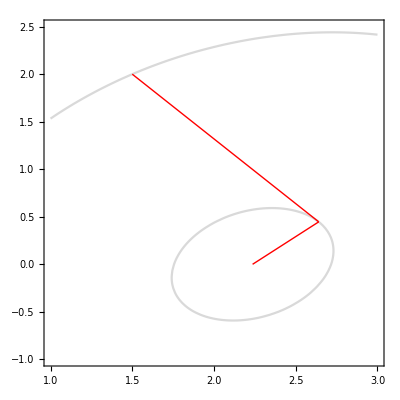

{2,57}

{2.23608,-0.0000216119}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1,3},{y,-1,2.5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
```

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1,3},{y,-1,2.5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps2f1p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

-Graphics-

{2,57}

{2.23608,-0.0000216119}

{2,85}

{2.23607,2.30647×10^-8}

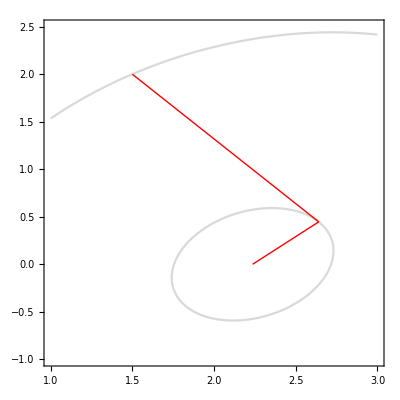

{2,57}

{2.23605,0.0000548154}

{2,85}

{2.23607,2.30647×10^-8}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps1f1p2.txt","Table"];
K=Table[ContourPlot[F1[x,y]==F1[str[[i,1]],str[[i,2]]],{x,1,3},{y,-1,2.5},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps2f1p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

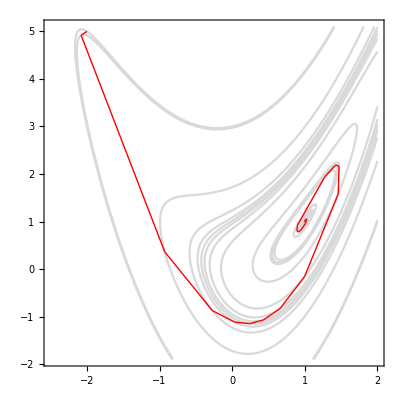

{27,816}

{0.994217,0.986296}

{53,2724}

{1.00001,1.00001}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-2.5,2},{y,-1.9,5.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps2f2p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

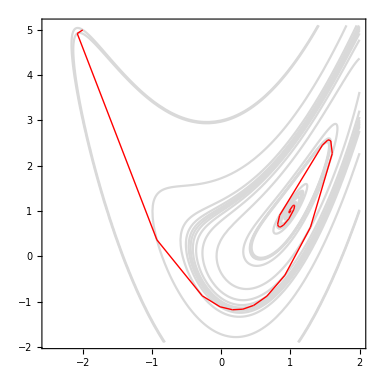

{38,1142}

{1.00656,1.01456}

{79,4051}

{1.00001,1.00002}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-2.5,2},{y,-1.9,5.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps2f2p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

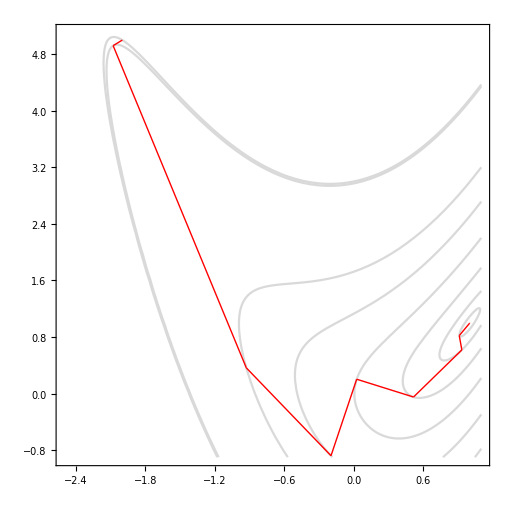

{9,270}

{0.999648,0.99928}

{10,459}

{1,1}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps1f2p1.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,-2.5,1.1},{y,-0.9,5.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps2f2p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

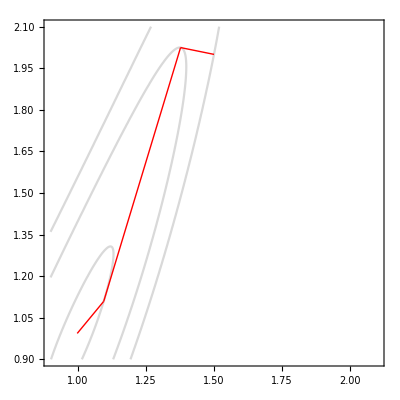

{3,94}

{0.998009,0.993552}

{8,437}

{1,1.}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps1f2p2.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,2.1},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps2f2p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

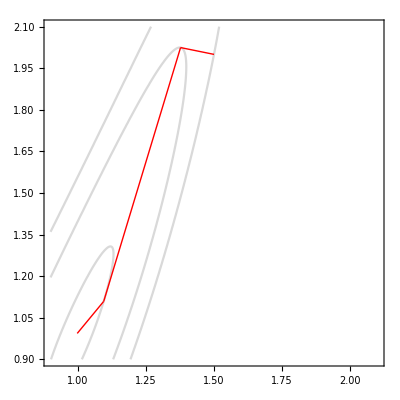

{3,94}

{0.998012,0.993559}

{8,437}

{1,1.}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps1f2p2.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,2.1},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps2f2p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

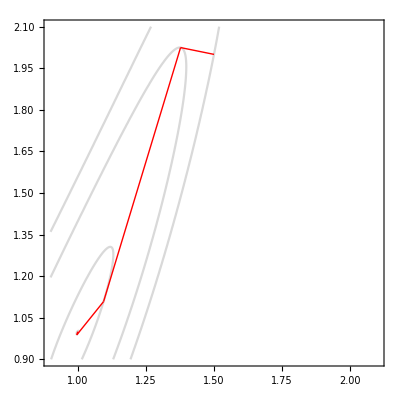

{4,131}

{0.999902,0.999876}

{5,246}

{1.,0.999999}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps1f2p2.txt","Table"];
K=Table[ContourPlot[F2[x,y]==F2[str[[i,1]],str[[i,2]]],{x,0.9,2.1},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps2f2p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

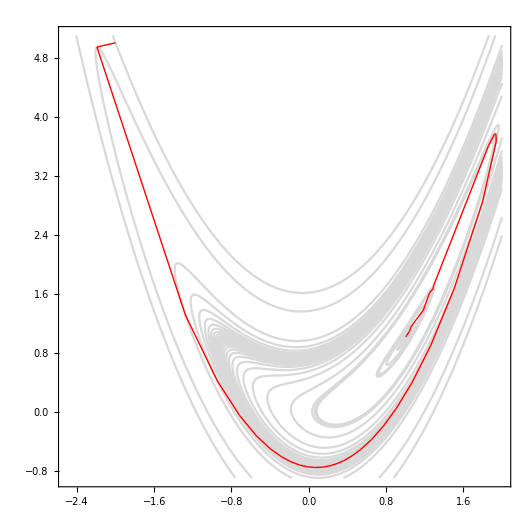

{41,1004}

{1.00614,1.01156}

{50,2499}

{0.999996,0.999992}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps1f3p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-2.5,2},{y,-0.9,5.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps2f3p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

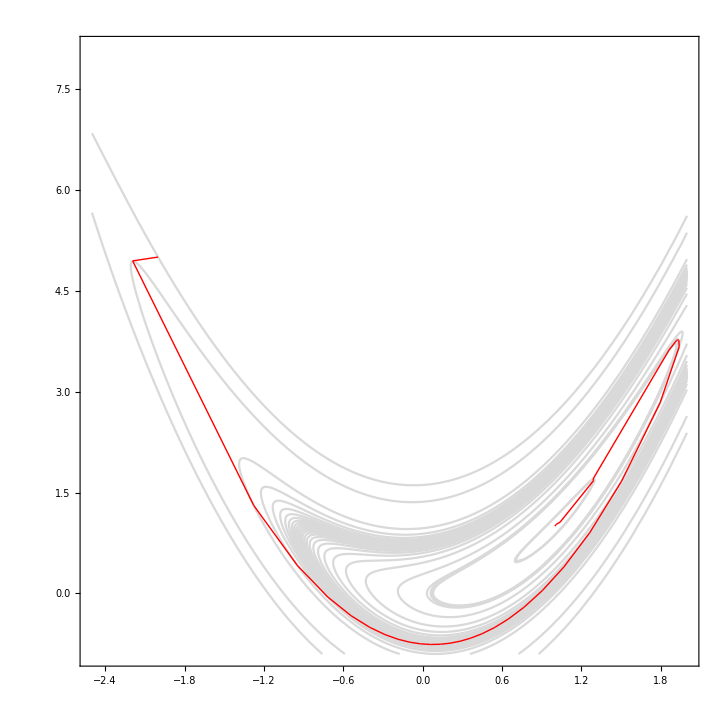

{38,920}

{1.0015,1.00233}

{123,6101}

{1.00001,1.00002}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps1f3p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-2.5,2},{y,-0.9,8.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps2f3p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

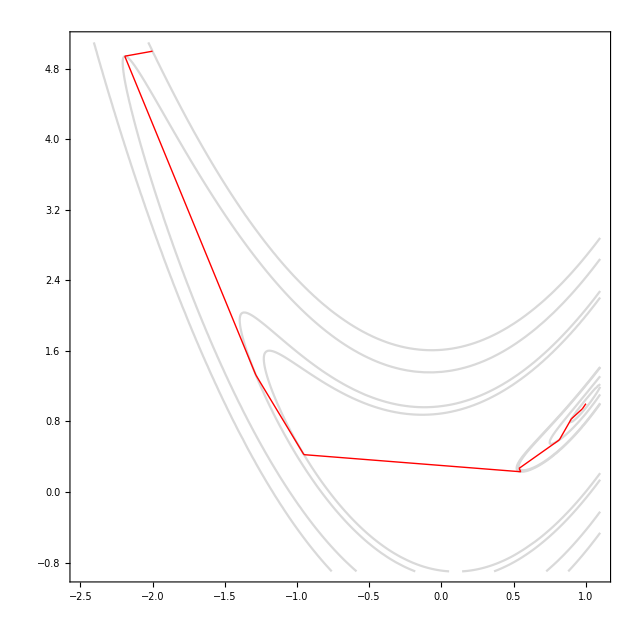

{10,284}

{1.00093,1.00136}

{14,611}

{1,1.}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps1f3p1.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,-2.5,1.1},{y,-0.9,5.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps2f3p1.txt","Table"];
str[[1]]
str[[Length[str]]]
```

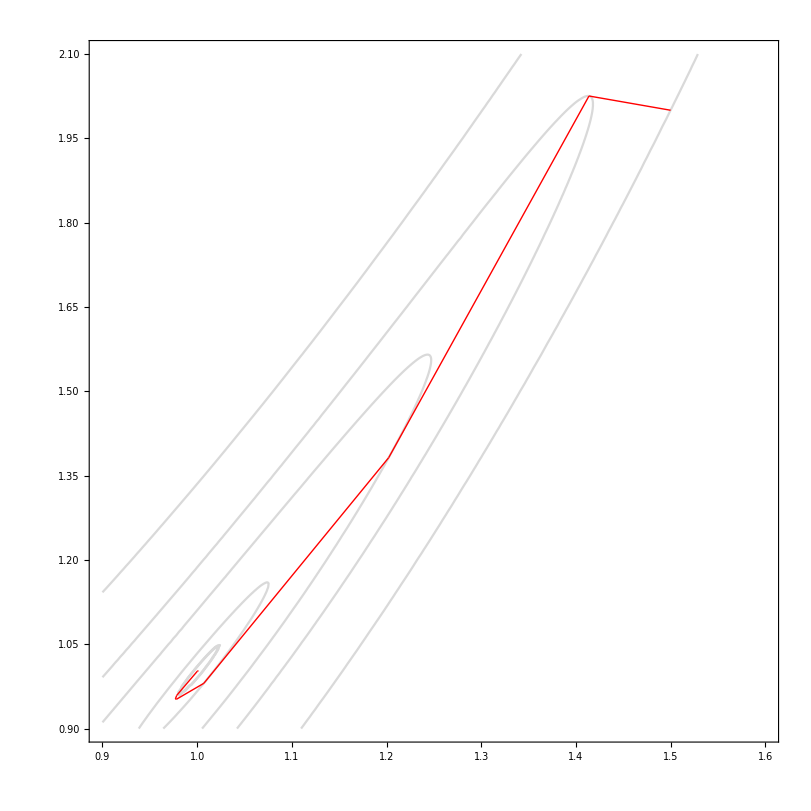

{8,255}

{1.00021,1.00213}

{16,836}

{1.00001,1.00001}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps1f3p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
str=Import["D:/1/MOVI lab/lab3/lab3/Soprgradeps2f3p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

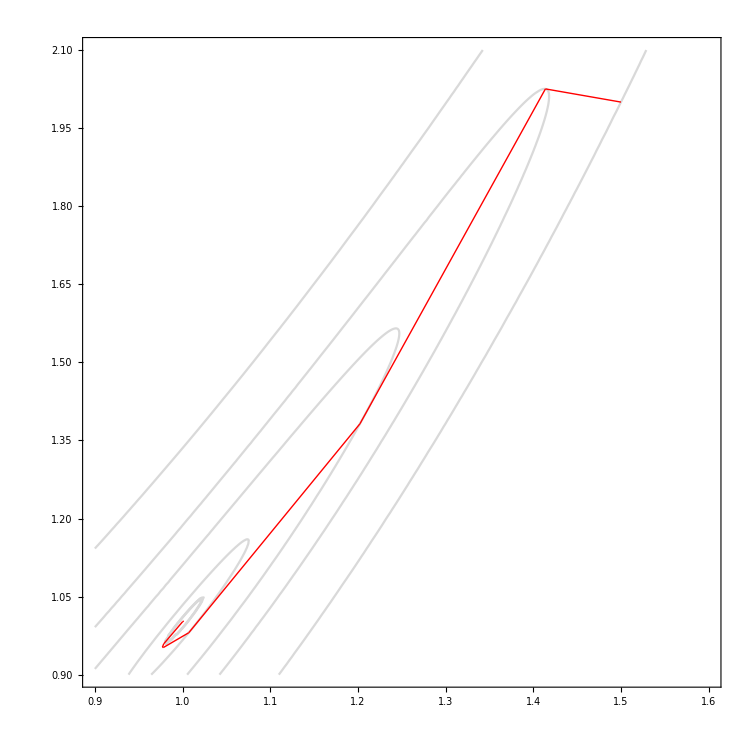

{8,255}

{1.00021,1.00213}

{16,836}

{1.00001,1.00001}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps1f3p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradFReps2f3p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```

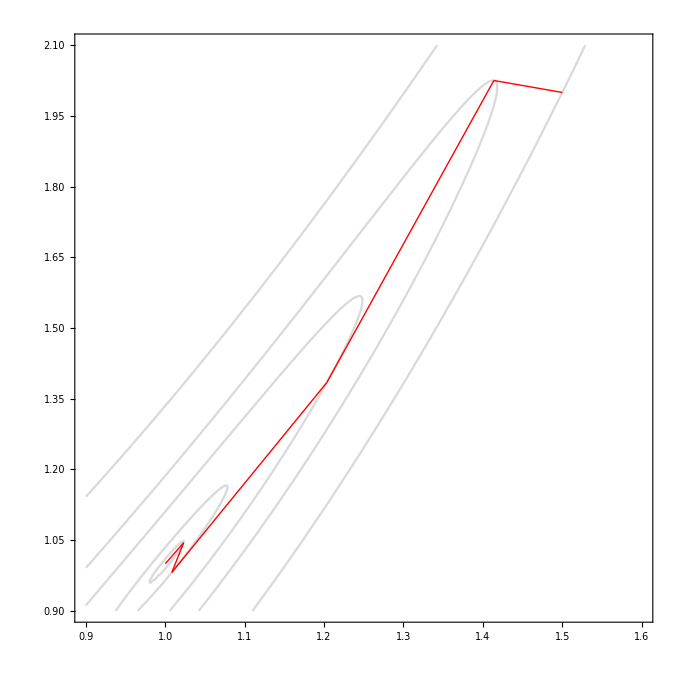

{5,145}

{1.02312,1.04466}

{7,332}

{1,1}

```mathematica
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps1f3p2.txt","Table"];
K=Table[ContourPlot[F3[x,y]==F3[str[[i,1]],str[[i,2]]],{x,0.9,1.6},{y,0.9,2.1},MaxRecursion->3,ContourStyle->LightGray],{i,2,Length[str]}];
M=Table[Graphics[{Arrowheads[0.02],Red,Line[{str[[i]],str[[i+1]]}]}],{i,2,Length[str]-1}];
Show[K,M]
str[[1]]
str[[Length[str]-1]]
str=Import["D:/1/MOVI lab/lab3/lab3/SoprgradPReps2f3p2.txt","Table"];
str[[1]]
str[[Length[str]]]
```